# Cellular Automaton Transients

"THE CHALLENGE"

Find the length of a transient in a cellular automaton evolution.

## More Details

For a finite initial condition, a cellular automaton eventually repeats, but there may be a transient consisting of the rows before the repetition starts.

For example, this evolution starts repeating on the fourth row (after three steps), so its transient length is three:

```mathematica
CellularAutomaton[45,{0,0,1,1},6]
```

{{0,0,1,1},{0,0,1,0},{1,0,1,0},{1,1,1,1},{0,0,0,0},{1,1,1,1},{0,0,0,0}}

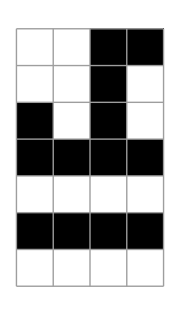

```mathematica
ArrayPlot[%,Mesh->True,ImageSize->Small]
```

## What Your Function Should Do

Write a function called CATransientLength that takes as input a rule number, an initial condition and the maximum number of steps to perform. It should return the length of the smallest transient, making the periodic part start as early as possible.

```mathematica
CATransientLength[45,{0,0,1,1},6]
```

3

```mathematica
CATransientLength[30,{1,1,0,0,0,0,1,0,0,0},100]
```

24

```mathematica
CATransientLength[149,{0,0,1,1,1},1000]
```

5

### More Examples

If there are not enough steps to span the transient and then the period twice, the entire evolution seen is viewed as transient:

```mathematica
CATransientLength[169,{0,1,1,1,1,0,0,1,1,1},50]
```

51

Rule 169 with this initial condition eventually repeats with period 205. Specifying the maximum steps to be large enough gives the true transient:

```mathematica
CATransientLength[169,{0,1,1,1,1,0,0,1,1,1},412]
```

413

This is large enough (2×205+4-1=413):

```mathematica
CATransientLength[169,{0,1,1,1,1,0,0,1,1,1},413]
```

4

This configuration starts out periodic and hence has no transient:

```mathematica
CATransientLength[150,{0,0,0,1,0,0,0},50]
```

0

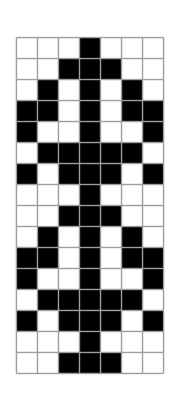

```mathematica
ArrayPlot[CellularAutomaton[150,{0,0,0,1,0,0,0},15],Mesh->True,ImageSize->Small]
```

## Things You May Find Useful

"Elementary Cellular Automaton »"http://mathworld.wolfram.com/ElementaryCellularAutomaton.htmlNonehttp://mathworld.wolfram.com/ElementaryCellularAutomaton.htmlHyperlinkText0.21176470588235294

A New Kind of Science

"SCRATCH AREA"

```mathematica
rn=181
```

181

```mathematica
init={1,0,0,1,0,0,1,0,0,0,0,0,1,0,1,1,0,1}
```

{1,0,0,1,0,0,1,0,0,0,0,0,1,0,1,1,0,1}

```mathematica
t=144
```

144

```mathematica
result=CellularAutomaton[rn,init,t]
```

{{1,0,0,1,0,0,1,0,0,0,0,0,1,0,1,1,0,1},{0,1,0,1,1,0,1,1,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,0,1,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,0,1,0,1,1,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,0,1,0,1,0,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,1,1,1,1,0,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,0,1,0,1,1,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,0},{0,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1},{1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0},{0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1},{1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,0},{1,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,1,1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1},{0,1,0,1,1,0,1,0,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,0,1,1,1,0,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,1,1,0,1,1,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,0,1,0,1,0,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,1,1,1,1,0,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,1,1,0,1,1,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,0,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,1},{1,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1,0,1},{1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0},{1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1},{1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1},{0,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,1,1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,0,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,1,1,0,1,1,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,0,1,0,1,0,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,1,1,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,1,1,0,1,1,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,1,1,0,1,0,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,0,1,1,1,0,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,1,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,0},{0,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1,1,1},{1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0},{0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1},{1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,1},{0,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,0,1,0,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,1,1,1,1,0,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,1,1,0,1,1,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,0,1,1,1,0,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,0,1,0,1,1,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,1,1,1,1,0,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1},{1,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1,0,1},{1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0},{1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1},{1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,0},{1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,0,1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,1,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1},{0,1,0,1,1,0,1,1,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,0,1,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,0,1,0,1,1,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,0,1,0,1,0,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,1,1,1,1,0,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,0,1,0,1,1,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,0},{0,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1},{1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0},{0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1},{1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,0},{1,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,1,1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,0,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1},{0,1,0,1,1,0,1,0,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,0,1,1,1,0,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,1,1,0,1,1,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,0,1,0,1,0,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,1,1,1,1,0,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,1,1,0,1,1,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,0,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,1},{1,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1,0,1},{1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0},{1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1},{1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1},{0,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,1,1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,0,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,1,1,0,1,1,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,0,1,0,1,0,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,1,1,1,1,0,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,1,1,0,1,1,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,0,1,0,1,1,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,1,1,0,1,0,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,0,1,1,1,0,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,1,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,0},{0,1,0,1,0,0,1,0,1,1,0,1,1,0,1,1,1,1},{1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0},{0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1},{1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,1},{0,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,0,1,0,1,1,1,0,1,1,0,0,1,0},{0,1,1,0,1,1,1,1,0,1,0,1,0,0,1,0,1,1},{1,0,0,1,0,1,1,0,1,1,1,1,1,0,1,1,0,0},{1,1,0,1,1,0,0,1,0,1,1,1,0,1,0,0,1,0},{0,0,1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1},{1,0,1,1,0,1,1,0,0,1,1,1,0,1,0,1,0,0},{1,1,0,0,1,0,0,1,0,0,1,0,1,1,1,1,1,0},{0,0,1,0,1,1,0,1,1,0,1,1,0,1,1,1,0,1},{1,0,1,1,0,0,1,0,0,1,0,0,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1,1,0,1,1,1,1,0,1},{1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0,1,1},{1,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1,0,1},{1,0,1,1,1,0,1,1,0,0,1,0,0,1,0,1,1,0},{1,1,0,1,0,1,0,0,1,0,1,1,0,1,1,0,0,1},{1,0,1,1,1,1,1,0,1,1,0,0,1,0,0,1,0,0},{1,1,0,1,1,1,0,1,0,0,1,0,1,1,0,1,1,0},{0,0,1,0,1,0,1,1,1,0,1,1,0,0,1,0,0,1},{1,0,1,1,1,1,0,1,0,1,0,0,1,0,1,1,0,1}}

```mathematica
ArrayPlot[result,Mesh->True,ImageSize->Small]
```

-Graphics-

```mathematica
MemberQ[result[[3;;]],result[[2]]]
```

True

```mathematica
pointer = Position[result[[3;;]],result[[2]]][[1]][[1]]
```

72

```mathematica
pointer=pointer+2
```

74

```mathematica
pointer-2+pointer≤t
```

False

```mathematica
(*Solution 1*)
```

```mathematica
Module[{result=CellularAutomaton[rn,init,t]},
	l=t+1;
	i=1;
	(*需要补充验证是否在该序列中完成一个重复单元*)
	While[(!MemberQ[result[[i+1;;]],result[[i]]]||2*Position[result[[i+1;;]],result[[i]]][[1]][[1]]+i>t)&&i<l,i++];
	(*如果超出范围都没有找到，则按照返回t+1，即i*)
	If[i>t,i,i-1]
	]
```

145

```mathematica
(*Solution 2*)
```

```mathematica
Module[{result=CellularAutomaton[rn,init,t]},
	l=t+1;
	i=1;
	
	While[!MemberQ[result[[i+1;;]],result[[i]]]&&i<l,i++];
	(*需要补充验证是否在该序列中完成一个重复单元*)
	If[2*Position[result[[i+1;;]],result[[i]]][[1]][[1]]+i>t,i=t+1];
	(*如果超出范围都没有找到，则按照返回t+1，即i*)
	If[i>t,i,i-1]
	]
```

145

"ENTER YOUR CODE HERE"

```mathematica
CATransientLength[rn_Integer/;0≤rn≤255,init:{(0|1)..},t_Integer]:=Module[{result=CellularAutomaton[rn,init,t]},
	l=t+1;
	i=1;
	(*需要补充验证是否在该序列中完成一个重复单元*)
	While[(!MemberQ[result[[i+1;;]],result[[i]]]||2*Position[result[[i+1;;]],result[[i]]][[1]][[1]]+i>t)&&i<l,i++];
	(*如果超出范围都没有找到，则按照返回t+1，即i*)
	If[i>t,i,i-1]
	]
```

WolframAlphaQueryResults